```mathematica
Quantity[12,"Hours"]5 7 4
```

1680 h

```mathematica
Quantity[12,"USDollars"]5 7 4
```

1680 $

```mathematica
Quantity[12,"USDollars"]5 7
```

420 $

```mathematica
Series[Sin[x],{x,0,10}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11

```mathematica
Normal[x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^11]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880

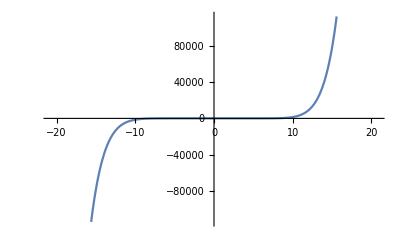

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-20.784609690826528,20.784609690826528}]
```

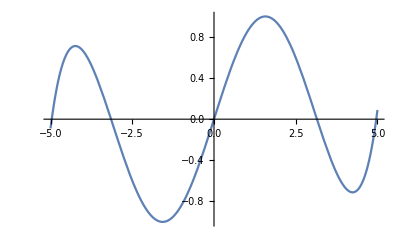

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-5,5}]
```

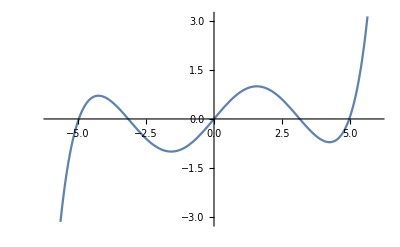

```mathematica
Plot[x-x^3/6+x^5/120-x^7/5040+x^9/362880,{x,-6,6}]
```

```mathematica
Plot[{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880},x]
```

Plot::pllim: Range specification x is not of the form {x, xmin, xmax}.

Plot[{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880},x]

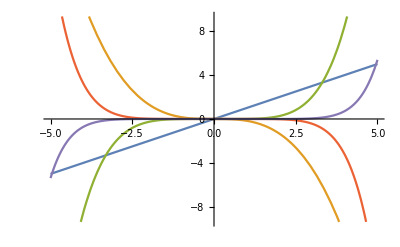

```mathematica
Plot[{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880},{x,-5,5}]
```

```mathematica
Abs[{x,-x^3/6,x^5/120,-x^7/5040,x^9/362880}]
```

{Abs[x],Abs[x]^3/6,Abs[x]^5/120,Abs[x]^7/5040,Abs[x]^9/362880}

```mathematica
FullSimplify[{Abs[x],Abs[x]^3/6,Abs[x]^5/120,Abs[x]^7/5040,Abs[x]^9/362880}/(Total@{Abs[x],Abs[x]^3/6,Abs[x]^5/120,Abs[x]^7/5040,Abs[x]^9/362880}),x∈Reals]
```

{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}

```mathematica
Map[Function[x,#]&,{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}]
```

{Function[x,362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)],Function[x,(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)],Function[x,(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)],Function[x,(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)],Function[x,x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]}

```mathematica
Map[
Normalize@{0,#''[x]}.Normalize@{0,#'[x]}&
,{Function[x,362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)],Function[x,(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)],Function[x,(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)],Function[x,(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)],Function[x,x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]}]
```

{-((120960 x+12096 x^3+432 x^5+8 x^7) ((725760 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(362880 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2 Abs[(120960 x+12096 x^3+432 x^5+8 x^7)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)] Abs[(725760 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(362880 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)]),((-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) (-(241920 x (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+120960/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+60480 x^2 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))))/(Abs[-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] Abs[-(241920 x (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+120960/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+60480 x^2 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))]),((-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) (-(24192 x^3 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(36288 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+3024 x^4 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))))/(Abs[-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] Abs[-(24192 x^3 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(36288 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+3024 x^4 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))]),((-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) (-(864 x^5 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(2160 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+72 x^6 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))))/(Abs[-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] Abs[-(864 x^5 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(2160 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+72 x^6 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))]),(((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) (-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)))/(Abs[(2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] Abs[-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])}

```mathematica
FullSimplify[
{-((120960 x+12096 x^3+432 x^5+8 x^7) ((725760 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(362880 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2 Abs[(120960 x+12096 x^3+432 x^5+8 x^7)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)] Abs[(725760 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(362880 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)]),((-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) (-(241920 x (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+120960/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+60480 x^2 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))))/(Abs[-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] Abs[-(241920 x (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+120960/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+60480 x^2 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))]),((-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) (-(24192 x^3 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(36288 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+3024 x^4 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))))/(Abs[-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] Abs[-(24192 x^3 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(36288 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+3024 x^4 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))]),((-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) (-(864 x^5 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(2160 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+72 x^6 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))))/(Abs[-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] Abs[-(864 x^5 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(2160 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+72 x^6 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))]),(((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) (-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)))/(Abs[(2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] Abs[-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])}
,x∈Reals]
```

{-Sign[x] Sign[-609638400+121927680 x^2+34836480 x^4+3225600 x^6+168336 x^8+5544 x^10+106 x^12+x^14],-Sign[x (-120960+1008 x^4+48 x^6+x^8) (43893964800-21946982400 x^2-4389396480 x^4-278691840 x^6-4644864 x^8+350784 x^10+25344 x^12+648 x^14+7 x^16)],Sign[x]^3 Sign[-362880-30240 x^2+36 x^6+x^8] Sign[-395045683200-32920473600 x^2+3657830400 x^4+627056640 x^6+34836480 x^8+864864 x^10+1296 x^12-324 x^14-5 x^16],-Sign[x]^5 Sign[-1088640-120960 x^2-3024 x^4+x^8] Sign[658409472000+124366233600 x^2+7315660800 x^4+x^8 (-17031168-762048 x^2-12096 x^4-24 x^6+x^8)],Sign[x]^7 Sign[17069875200+3962649600 x^2+345461760 x^4+13547520 x^6+193536 x^8-2856 x^10-116 x^12-x^14]}

```mathematica
{-Sign[x] Sign[-609638400+121927680 x^2+34836480 x^4+3225600 x^6+168336 x^8+5544 x^10+106 x^12+x^14],-Sign[x (-120960+1008 x^4+48 x^6+x^8) (43893964800-21946982400 x^2-4389396480 x^4-278691840 x^6-4644864 x^8+350784 x^10+25344 x^12+648 x^14+7 x^16)],Sign[x]^3 Sign[-362880-30240 x^2+36 x^6+x^8] Sign[-395045683200-32920473600 x^2+3657830400 x^4+627056640 x^6+34836480 x^8+864864 x^10+1296 x^12-324 x^14-5 x^16],-Sign[x]^5 Sign[-1088640-120960 x^2-3024 x^4+x^8] Sign[658409472000+124366233600 x^2+7315660800 x^4+x^8 (-17031168-762048 x^2-12096 x^4-24 x^6+x^8)],Sign[x]^7 Sign[17069875200+3962649600 x^2+345461760 x^4+13547520 x^6+193536 x^8-2856 x^10-116 x^12-x^14]}
```

```mathematica
Map[Function[x,Abs[#]]&,{362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8),x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)}]
```

{Function[x,Abs[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]}

```mathematica
FullSimplify[
Map[
Normalize@{0,#''[x]}.Normalize@{0,#'[x]}&
,{Function[x,Abs[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]}]
,x∈Reals]
```

$Aborted

```mathematica
Map[
Normalize@{0,#''[x]}.Normalize@{0,#'[x]}&
,{Function[x,Abs[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]],Function[x,Abs[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]}]
```

{-(((120960 x+12096 x^3+432 x^5+8 x^7) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((725760 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(362880 (120960+36288 x^2+2160 x^4+56 x^6) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(131681894400 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs''[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^4)))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2 Abs[((120960 x+12096 x^3+432 x^5+8 x^7) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)] Abs[(725760 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(362880 (120960+36288 x^2+2160 x^4+56 x^6) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(131681894400 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs''[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^4)])),((-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((-(241920 x (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+120960/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+60480 x^2 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(241920 x (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+120960/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+60480 x^2 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]),((-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((-(24192 x^3 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(36288 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+3024 x^4 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(24192 x^3 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(36288 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+3024 x^4 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]),((-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((-(864 x^5 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(2160 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+72 x^6 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(864 x^5 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(2160 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+72 x^6 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]),((-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] (((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]])}

```mathematica
FullSimplify[{-(((120960 x+12096 x^3+432 x^5+8 x^7) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((725760 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(362880 (120960+36288 x^2+2160 x^4+56 x^6) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(131681894400 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs''[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^4)))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2 Abs[((120960 x+12096 x^3+432 x^5+8 x^7) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)] Abs[(725760 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(362880 (120960+36288 x^2+2160 x^4+56 x^6) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(131681894400 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs''[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^4)])),((-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((-(241920 x (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+120960/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+60480 x^2 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(241920 x (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+120960/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+60480 x^2 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]),((-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((-(24192 x^3 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(36288 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+3024 x^4 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(24192 x^3 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(36288 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+3024 x^4 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]),((-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((-(864 x^5 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(2160 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+72 x^6 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(864 x^5 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(2160 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+72 x^6 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]),((-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] (((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]])}
,x∈Reals]
```

$Aborted

```mathematica
FullSimplify[((-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] (((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]])
,x∈Reals]
```

$Aborted

```mathematica
((-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] (((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]])/.Abs''->0
```

((-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 0[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 0[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]])

```mathematica
((-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] (((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]])/.Abs''[x]->0
```

((-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] (((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]])

```mathematica
((-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] (((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 0))/(Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 0])
```

(((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) (-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]^2)/(Abs[((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]])

```mathematica
Plot[{-(((120960 x+12096 x^3+432 x^5+8 x^7) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((725760 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(362880 (120960+36288 x^2+2160 x^4+56 x^6) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(131681894400 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs''[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^4)))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2 Abs[((120960 x+12096 x^3+432 x^5+8 x^7) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)] Abs[(725760 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(362880 (120960+36288 x^2+2160 x^4+56 x^6) Abs'[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(131681894400 (120960 x+12096 x^3+432 x^5+8 x^7)^2 Abs''[362880/(362880+60480 x^2+3024 x^4+72 x^6+x^8)])/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^4)])),((-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((-(241920 x (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+120960/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+60480 x^2 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(241920 x (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+120960/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+60480 x^2 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(60480 x^2 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(120960 x)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(60480 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]),((-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((-(24192 x^3 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(36288 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+3024 x^4 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(24192 x^3 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(36288 x^2)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+3024 x^4 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(3024 x^4 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(12096 x^3)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(3024 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]),((-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] ((-(864 x^5 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(2160 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+72 x^6 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[(-(864 x^5 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(2160 x^4)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)+72 x^6 (-(2 (-120960 x-12096 x^3-432 x^5-8 x^7) (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(120960+36288 x^2+2160 x^4+56 x^6)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2))) Abs'[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(72 x^6 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(432 x^5)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[(72 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]]),((-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)] (((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]))/(Abs[(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]] Abs[((2 x^8 (120960 x+12096 x^3+432 x^5+8 x^7)^2)/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^3)-(x^8 (120960+36288 x^2+2160 x^4+56 x^6))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)-(16 x^7 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(56 x^6)/(362880+60480 x^2+3024 x^4+72 x^6+x^8)) Abs'[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]+(-(x^8 (120960 x+12096 x^3+432 x^5+8 x^7))/((362880+60480 x^2+3024 x^4+72 x^6+x^8)^2)+(8 x^7)/(362880+60480 x^2+3024 x^4+72 x^6+x^8))^2 Abs''[x^8/(362880+60480 x^2+3024 x^4+72 x^6+x^8)]])},{x,-6,6}]
```

-Graphics-

```mathematica
ComplexPlot3D[Gamma[z],{z,-5-5I,5+5I}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[Gamma[z],{z,-5-5I,5+5I},PlotRange->Full]
```

-Graphics3D-

```mathematica
ComplexPlot3D[z^2,{z,-5-5I,5+5I}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[1/(1+z^2),{z,-5-5I,5+5I}]
```

-Graphics3D-

```mathematica
x^3-x
```

-x+x^3

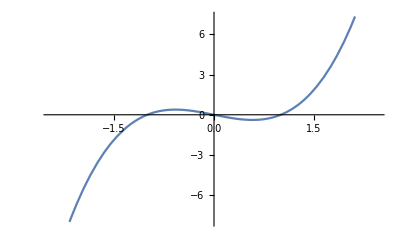

```mathematica
Plot[-x+x^3,{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
Map[Function[x,#]&,Abs[{x^3,x}]]
```

{Function[x,Abs[x]^3],Function[x,Abs[x]]}

```mathematica
Map[Normalize@{0,#''[x]}.Normalize@{1,#'[x]}&,
,Map[Function[x,#]&,Abs[{x^3,x}]]]
```

Map::level: Level specification {Function[x,Abs[x]^3],Function[x,Abs[x]]} is not of the form n, {n}, or {m, n}.

Map[Normalize[{0,#1''[x]}].Normalize[{1,#1'[x]}]&,Null,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]

```mathematica
Map[
Function[y,Normalize@{0,y''[x]}.Normalize@{1,y'[x]}],
,Map[Function[x,#]&,Abs[{x^3,x}]]]
```

Map::level: Level specification {Function[x,Abs[x]^3],Function[x,Abs[x]]} is not of the form n, {n}, or {m, n}.

Map[Function[y,Normalize[{0,y''[x]}].Normalize[{1,y'[x]}]],Null,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]

```mathematica
Map[Function[x,#]&,Abs[{x^3,x}]]
```

{Function[x,Abs[x]^3],Function[x,Abs[x]]}

```mathematica
Map[
Function[y,Normalize@{0,y''[x]}.Normalize@{1,y'[x]}],
,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]
```

Map::level: Level specification {Function[x,Abs[x]^3],Function[x,Abs[x]]} is not of the form n, {n}, or {m, n}.

Map[Function[y,Normalize[{0,y''[x]}].Normalize[{1,y'[x]}]],Null,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]

```mathematica
Map[
Function[y,Normalize@{0,y''}.Normalize@{1,y'}],
,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]
```

Map::level: Level specification {Function[x,Abs[x]^3],Function[x,Abs[x]]} is not of the form n, {n}, or {m, n}.

Map[Function[y,Normalize[{0,y''}].Normalize[{1,y'}]],Null,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]

```mathematica
Map[
Function[y,y],
,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]
```

Map::level: Level specification {Function[x,Abs[x]^3],Function[x,Abs[x]]} is not of the form n, {n}, or {m, n}.

Map[Function[y,y],Null,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]

```mathematica
Map[
#&,
,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]
```

Map::level: Level specification {Function[x,Abs[x]^3],Function[x,Abs[x]]} is not of the form n, {n}, or {m, n}.

Map[#1&,Null,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]

```mathematica
Map[
Function[y,Normalize@{0,y''}.Normalize@{1,y'}]
,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]
```

{(Function[x,3 Abs[x]^2 Abs'[x]] Function[x,(Abs')'[x] (3 Abs[x]^2)+(2 Abs[x] Abs'[x]) (3 Abs'[x])])/(√(1+Abs[Function[x,3 Abs[x]^2 Abs'[x]]]^2) Abs[Function[x,(Abs')'[x] (3 Abs[x]^2)+(2 Abs[x] Abs'[x]) (3 Abs'[x])]]),(Function[x,Abs'[x]] Function[x,(Abs')'[x]])/(√(1+Abs[Function[x,Abs'[x]]]^2) Abs[Function[x,(Abs')'[x]]])}

```mathematica
FullSimplify[
Map[
Function[y,Normalize@{0,y''}.Normalize@{1,y'}]
,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]
,x∈Reals]
```

{(Function[x,3 Abs[x]^2 Abs'[x]] Sign[Function[x,(Abs')'[x] (3 Abs[x]^2)+(2 Abs[x] Abs'[x]) (3 Abs'[x])]])/(√(1+Abs[Function[x,3 Abs[x]^2 Abs'[x]]]^2)),(Function[x,Abs'[x]] Sign[Function[x,(Abs')'[x]]])/(√(1+Abs[Function[x,Abs'[x]]]^2))}

```mathematica
FullSimplify[
Map[
Function[y,Normalize@{0,y''[x]}.Normalize@{1,y'[x]}]
,{Function[x,Abs[x]^3],Function[x,Abs[x]]}]
,x∈Reals]
```

{(3 x^3 (2 Sign[x]^2+Abs[x] Abs''[x]))/(Abs[x (2 Sign[x]+x Abs''[x])] √(1+9 x^4 Sign[x]^2)),(Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2))}

```mathematica
FullSimplify[{(3 x^3 (2 Sign[x]^2+Abs[x] Abs''[x]))/(Abs[x (2 Sign[x]+x Abs''[x])] √(1+9 x^4 Sign[x]^2)),(Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2))}/(Total@{(3 x^3 (2 Sign[x]^2+Abs[x] Abs''[x]))/(Abs[x (2 Sign[x]+x Abs''[x])] √(1+9 x^4 Sign[x]^2)),(Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2))}),x∈Reals]
```

{Piecewise[{{1, x==0}, {1/(1+(√(1+9 x^4) Sign[Abs''[x]])/(3 √2 x^2 Sign[2-x Abs''[x]])), x<0}, {1/(1+(√(1+9 x^4) Sign[Abs''[x]])/(3 √2 x^2 Sign[2+x Abs''[x]])), True}}],(Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2) ((Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2))+(3 x^3 (2 Sign[x]^2+Abs[x] Abs''[x]))/(Abs[x (2 Sign[x]+x Abs''[x])] √(1+9 x^4 Sign[x]^2))))}

```mathematica
{(3 x^3 (2 Sign[x]^2+Abs[x] 0))/(Abs[x (2 Sign[x]+x 0)] √(1+9 x^4 Sign[x]^2)),(Sign[x] Sign[0])/(√(1+Sign[x]^2))}
```

{(3 x^3 Sign[x]^2)/(Abs[x Sign[x]] √(1+9 x^4 Sign[x]^2)),0}

```mathematica
Plot[{Piecewise[{{1, x==0}, {1/(1+(√(1+9 x^4) Sign[Abs''[x]])/(3 √2 x^2 Sign[2-x Abs''[x]])), x<0}, {1/(1+(√(1+9 x^4) Sign[Abs''[x]])/(3 √2 x^2 Sign[2+x Abs''[x]])), True}}],(Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2) ((Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2))+(3 x^3 (2 Sign[x]^2+Abs[x] Abs''[x]))/(Abs[x (2 Sign[x]+x Abs''[x])] √(1+9 x^4 Sign[x]^2))))},x∈Reals]
```

Plot::idomdim: x∈ does not have a valid dimension as a plotting domain.

Plot[{Piecewise[{{1, x==0}, {1/(1+(√(1+9 x^4) Sign[Abs''[x]])/(3 √2 x^2 Sign[2-x Abs''[x]])), x<0}, {1/(1+(√(1+9 x^4) Sign[Abs''[x]])/(3 √2 x^2 Sign[2+x Abs''[x]])), True}}],(Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2) ((Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2))+(3 x^3 (2 Sign[x]^2+Abs[x] Abs''[x]))/(Abs[x (2 Sign[x]+x Abs''[x])] √(1+9 x^4 Sign[x]^2))))},x∈ℝ]

```mathematica
Plot[{Piecewise[{{1, x==0}, {1/(1+(√(1+9 x^4) Sign[Abs''[x]])/(3 √2 x^2 Sign[2-x Abs''[x]])), x<0}, {1/(1+(√(1+9 x^4) Sign[Abs''[x]])/(3 √2 x^2 Sign[2+x Abs''[x]])), True}}],(Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2) ((Sign[x] Sign[Abs''[x]])/(√(1+Sign[x]^2))+(3 x^3 (2 Sign[x]^2+Abs[x] Abs''[x]))/(Abs[x (2 Sign[x]+x Abs''[x])] √(1+9 x^4 Sign[x]^2))))},{x,-5,5}]
```

-Graphics-

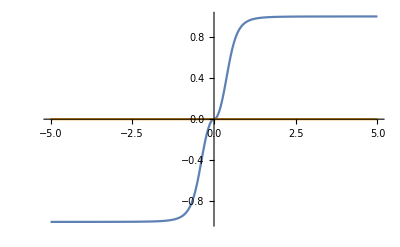

```mathematica
Plot[{(3 x^3 Sign[x]^2)/(Abs[x Sign[x]] √(1+9 x^4 Sign[x]^2)),0},{x,-5,5}]
```

```mathematica
Abs[D[{x,x^3},x]]
```

{1,3 Abs[x]^2}

```mathematica
FullSimplify[{1,3 Abs[x]^2}/(Total@{1,3 Abs[x]^2}),x∈Reals]
```

{1/(1+3 x^2),(3 x^2)/(1+3 x^2)}

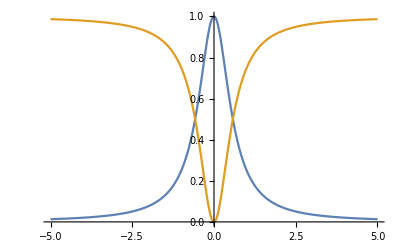

```mathematica
Plot[{1/(1+3 x^2),(3 x^2)/(1+3 x^2)},{x,-5,5}]
```

```mathematica
Abs[{x,x^3}]
```

{Abs[x],Abs[x]^3}

```mathematica
FullSimplify[{Abs[x],Abs[x]^3}/(Total@{Abs[x],Abs[x]^3}),x∈Reals]
```

{1/(1+x^2),x^2/(1+x^2)}

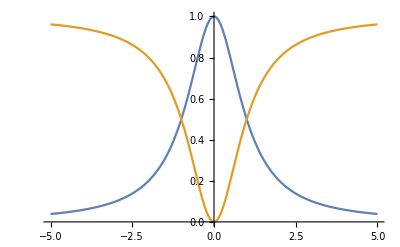

```mathematica
Plot[{1/(1+x^2),x^2/(1+x^2)},{x,-5,5}]
```

```mathematica
{Plot[{1/(1+3 x^2),(3 x^2)/(1+3 x^2)},{x,-5,5}],Plot[{1/(1+x^2),x^2/(1+x^2)},{x,-5,5}]}
```

{-Graphics-,-Graphics-}

```mathematica
{1/(1+x^2),x^2/(1+x^2)}^2+{1/(1+3 x^2),(3 x^2)/(1+3 x^2)}x
```

{1/((1+x^2)^2)+x/(1+3 x^2),x^4/((1+x^2)^2)+(3 x^3)/(1+3 x^2)}

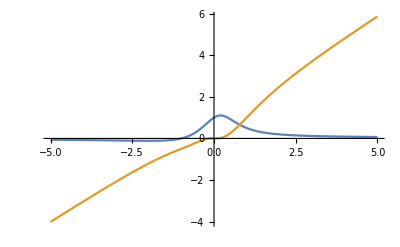

```mathematica
Plot[{1/((1+x^2)^2)+x/(1+3 x^2),x^4/((1+x^2)^2)+(3 x^3)/(1+3 x^2)},{x,-5,5}]
```

```mathematica
FullSimplify[Normalize@{x,x^3-x}.Normalize@{x,x^3},x∈Reals]
```

(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))

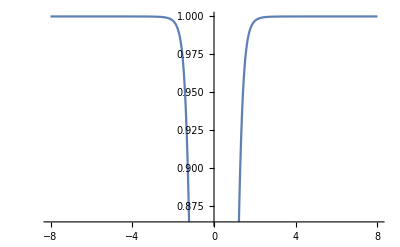

```mathematica
Plot[(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4))),{x,-8,8}]
```

```mathematica
FullSimplify[Abs[Normalize@{x,x^3-x}.Normalize@{x,x^3}],x∈Reals]
```

(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))

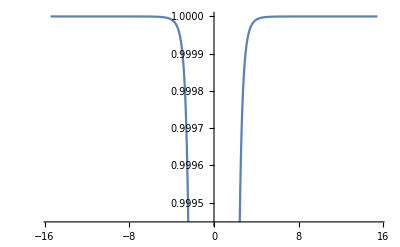

```mathematica
Plot[(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4))),{x,-15.443212101114199,15.443212101114199}]
```

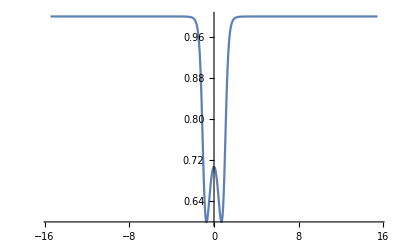

```mathematica
Plot[(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4))),{x,-15.443212101114199,15.443212101114199},PlotRange->Full]
```

```mathematica
FullSimplify[Abs[Normalize@{x,x^3-x}.Normalize@{x,-x}],x∈Reals]
```

Abs[-2+x^2]/(√2 √(2-2 x^2+x^4))

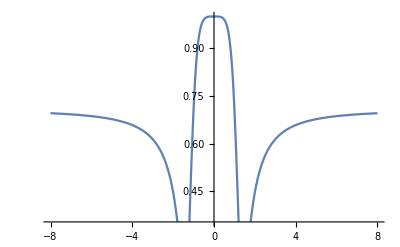

```mathematica
Plot[Abs[-2+x^2]/(√2 √(2-2 x^2+x^4)),{x,-8,8}]
```

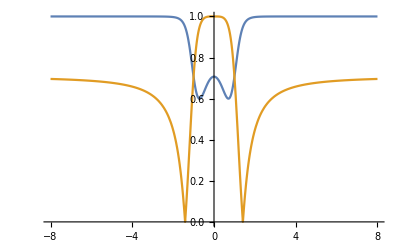

```mathematica
Plot[{(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4))),Abs[-2+x^2]/(√2 √(2-2 x^2+x^4))},{x,-8,8}]
```

```mathematica
FullSimplify[Total@{(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4))),Abs[-2+x^2]/(√2 √(2-2 x^2+x^4))}==1,x∈Reals]
```

(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))+Abs[-2+x^2]/(√2 √(2-2 x^2+x^4))==1

```mathematica
Reduce[(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))+Abs[-2+x^2]/(√2 √(2-2 x^2+x^4))==1]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))+Abs[-2+x^2]/(√2 √(2-2 x^2+x^4))==1]

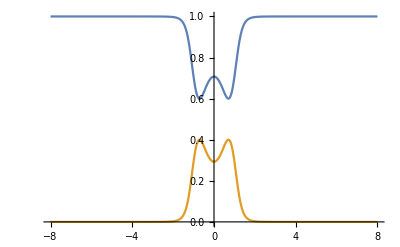

```mathematica
Plot[{(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4))),1-(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))},{x,-8,8}]
```

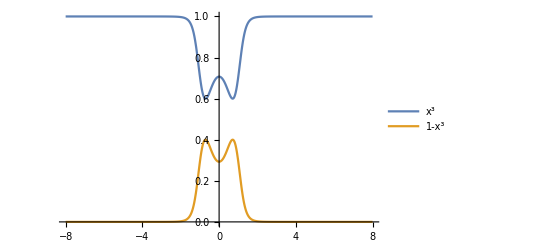

```mathematica
Plot[{(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4))),1-(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))},{x,-8,8},PlotLegends->{x^3,1-x^3}]
```

```mathematica
(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))==Normalize@{x,x^3-x}.Normalize@{x,x^3}+g[x]
```

(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))==x^2/(√(Abs[x]^2+Abs[x]^6) √(Abs[x]^2+Abs[-x+x^3]^2))+(x^3 (-x+x^3))/(√(Abs[x]^2+Abs[x]^6) √(Abs[x]^2+Abs[-x+x^3]^2))+g[x]

```mathematica
FullSimplify[(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))==Normalize@{x,x^3-x}.Normalize@{x,x^3}+g[x],{x,g[x]}∈Reals]
```

g[x]==0

```mathematica
(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))==Normalize@{x,x^3-x}.Normalize@{x,x^3}+Normalize@{x,x^3-x}.Normalize@{x,g[x]}
```

(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))==x^2/(√(Abs[x]^2+Abs[x]^6) √(Abs[x]^2+Abs[-x+x^3]^2))+(x^3 (-x+x^3))/(√(Abs[x]^2+Abs[x]^6) √(Abs[x]^2+Abs[-x+x^3]^2))+x^2/(√(Abs[x]^2+Abs[-x+x^3]^2) √(Abs[x]^2+Abs[g[x]]^2))+((-x+x^3) g[x])/(√(Abs[x]^2+Abs[-x+x^3]^2) √(Abs[x]^2+Abs[g[x]]^2))

```mathematica
FullSimplify[(1-x^2+x^4)/(√((1+x^4) (2-2 x^2+x^4)))==Normalize@{x,x^3-x}.Normalize@{x,x^3}+Normalize@{x,x^3-x}.Normalize@{x,g[x]},{x,g[x]}∈Reals]
```

(x+(-1+x^2) g[x])/Sign[x]==0

```mathematica
Reduce[(x+(-1+x^2) g[x])/Sign[x]==0]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(x+(-1+x^2) g[x])/Sign[x]==0]

```mathematica
Solve[(x+(-1+x^2) g[x])/Sign[x]==0,g[x],Reals]
```

{{g[x]→-x/(-1+x^2)}}

```mathematica
g[x]/.{{g[x]->-x/(-1+x^2)}}
```

{-x/(-1+x^2)}

```mathematica
First[{-x/(-1+x^2)}]
```

-x/(-1+x^2)

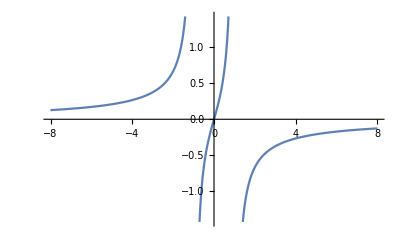

```mathematica
Plot[-x/(-1+x^2),{x,-8,8}]
```

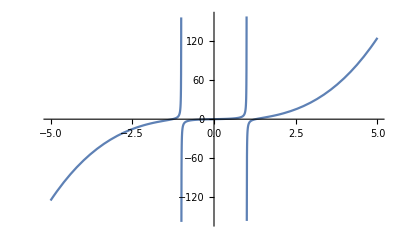

```mathematica
Plot[x^3-x/(-1+x^2),{x,-5,5}]
```